### Start choosing the example:

```mathematica
t=21;
beta = 1;
A =0.5;
g[x]
```

x

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesData.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},Adjacency Matrix→{{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,I1},{2,I2}},Exit Vertices and Terminal Costs→{{13,U1},{14,U2},{15,U3}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->1000,I2->1500,U1->10,U2->100, U3->50}];//Timing
MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort
MFGEquations["uvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort
```

DataToEquations: Triangle inequalities for switching costs: {}
DataToEquations: Reduced: True

The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

$Aborted

<|{1,1->3}→0,{1,en830->1}→1000,{2,2->3}→0,{2,en831->2}→1500,{3,1->3}→1000,{3,2->3}→1500,{3,3->4}→0,{4,3->4}→2500,{4,4->5}→0,{5,4->5}→2500,{5,5->6}→0,{6,5->6}→2500,{6,6->7}→0,{6,6->8}→0,{6,6->9}→0,{7,6->7}→2630/3,{7,7->ex832}→0,{8,6->8}→2360/3,{8,8->ex833}→0,{9,6->9}→2510/3,{9,9->ex834}→0,{en830,en830->1}→0,{en831,en831->2}→0,{ex832,7->ex832}→2630/3,{ex833,8->ex833}→2360/3,{ex834,9->ex834}→2510/3|>

<|{1,1->3}→28160/3,{1,en830->1}→28160/3,{2,2->3}→29660/3,{2,en831->2}→29660/3,{3,1->3}→25160/3,{3,2->3}→25160/3,{3,3->4}→25160/3,{4,3->4}→17660/3,{4,4->5}→17660/3,{5,4->5}→10160/3,{5,5->6}→10160/3,{6,5->6}→2660/3,{6,6->7}→2660/3,{6,6->8}→2660/3,{6,6->9}→2660/3,{7,6->7}→10,{7,7->ex832}→10,{8,6->8}→100,{8,8->ex833}→100,{9,6->9}→50,{9,9->ex834}→50,{en830,en830->1}→28160/3,{en831,en831->2}→29660/3,{ex832,7->ex832}→10,{ex833,8->ex833}→100,{ex834,9->ex834}→50|>

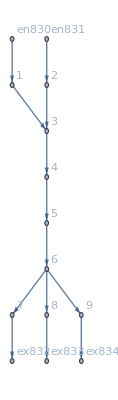

```mathematica
MFGEquations["FG"]
```

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j835-j848-u893+u906==987.414&&j836-j849-u894+u907==1485.59&&j837-j850-u895+u908==2482.91&&j838-j851-u896+u909==2482.91&&j839-j852-u897+u910==2482.91&&j840-j853-u898+u911==864.622&&j841-j854-u899+u912==775.05&&j842-j855-u900+u913==824.809

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0129697

FRX1: nonlinear: 
j835-j848-u893+u906==987.414&&j836-j849-u894+u907==1485.59&&j837-j850-u895+u908==2482.91&&j838-j851-u896+u909==2482.91&&j839-j852-u897+u910==2482.91&&j840-j853-u898+u911==907.556&&j841-j854-u899+u912==728.841&&j842-j855-u900+u913==828.108

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0129014

FRX1: nonlinear: 
j835-j848-u893+u906==987.414&&j836-j849-u894+u907==1485.59&&j837-j850-u895+u908==2482.91&&j838-j851-u896+u909==2482.91&&j839-j852-u897+u910==2482.91&&j840-j853-u898+u911==950.294&&j841-j854-u899+u912==682.866&&j842-j855-u900+u913==831.384

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0128305

FRX1: nonlinear: 
j835-j848-u893+u906==987.414&&j836-j849-u894+u907==1485.59&&j837-j850-u895+u908==2482.91&&j838-j851-u896+u909==2482.91&&j839-j852-u897+u910==2482.91&&j840-j853-u898+u911==992.837&&j841-j854-u899+u912==637.131&&j842-j855-u900+u913==834.631

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0127569

FRX1: nonlinear: 
j835-j848-u893+u906==987.414&&j836-j849-u894+u907==1485.59&&j837-j850-u895+u908==2482.91&&j838-j851-u896+u909==2482.91&&j839-j852-u897+u910==2482.91&&j840-j853-u898+u911==1035.19&&j841-j854-u899+u912==591.64&&j842-j855-u900+u913==837.845

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0126803

FRX1: nonlinear: 
j835-j848-u893+u906==987.414&&j836-j849-u894+u907==1485.59&&j837-j850-u895+u908==2482.91&&j838-j851-u896+u909==2482.91&&j839-j852-u897+u910==2482.91&&j840-j853-u898+u911==1077.34&&j841-j854-u899+u912==546.401&&j842-j855-u900+u913==841.02

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0126005

FRX1: nonlinear: 
j835-j848-u893+u906==987.414&&j836-j849-u894+u907==1485.59&&j837-j850-u895+u908==2482.91&&j838-j851-u896+u909==2482.91&&j839-j852-u897+u910==2482.91&&j840-j853-u898+u911==1119.3&&j841-j854-u899+u912==501.421&&j842-j855-u900+u913==844.15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0125173

FRX1: nonlinear: 
j835-j848-u893+u906==987.414&&j836-j849-u894+u907==1485.59&&j837-j850-u895+u908==2482.91&&j838-j851-u896+u909==2482.91&&j839-j852-u897+u910==2482.91&&j840-j853-u898+u911==1161.06&&j841-j854-u899+u912==456.709&&j842-j855-u900+u913==847.229

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0124304

FRX1: nonlinear: 
j835-j848-u893+u906==987.414&&j836-j849-u894+u907==1485.59&&j837-j850-u895+u908==2482.91&&j838-j851-u896+u909==2482.91&&j839-j852-u897+u910==2482.91&&j840-j853-u898+u911==1202.63&&j841-j854-u899+u912==412.278&&j842-j855-u900+u913==850.251

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0123394

FRX1: nonlinear: 
j835-j848-u893+u906==987.414&&j836-j849-u894+u907==1485.59&&j837-j850-u895+u908==2482.91&&j838-j851-u896+u909==2482.91&&j839-j852-u897+u910==2482.91&&j840-j853-u898+u911==1243.99&&j841-j854-u899+u912==368.141&&j842-j855-u900+u913==853.207

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0122436

<|j835→1000,j836→1500,j837→2500,j838→2500,j839→2500,j840→1298.88,j841→333.029,j842→868.095,j843→1298.88,j844→333.029,j845→868.095,j846→1000,j847→1500,j848→0,j849→0,j850→0,j851→0,j852→0,j853→0,j854→0,j855→0,j856→0,j857→0,j858→0,j859→0,j860→0,jt861→0,jt862→1000,jt863→0,jt864→1500,jt865→0,jt866→1000,jt867→0,jt868→1500,jt869→0,jt870→0,jt871→2500,jt872→0,jt873→2500,jt874→0,jt875→1298.88,jt876→333.029,jt877→868.095,jt878→0,jt879→0,jt880→0,jt881→0,jt882→0.,jt883→0.,jt884→0,jt885→0.,jt886→0.,jt887→1298.88,jt888→0,jt889→333.029,jt890→0,jt891→868.095,jt892→0,u893→128.744,u894→130.569,u895→116.158,u896→99.0681,u897→81.978,u898→64.888,u899→64.888,u900→64.888,u901→10,u902→100,u903→50,u904→128.744,u905→130.569,u906→116.158,u907→116.158,u908→99.0681,u909→81.978,u910→64.888,u911→10.,u912→100.,u913→50.,u914→10,u915→100,u916→50,u917→128.744,u918→130.569|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j835-j848-u893+u906==0&&j836-j849-u894+u907==0&&j837-j850-u895+u908==0&&j838-j851-u896+u909==0&&j839-j852-u897+u910==0&&j840-j853-u898+u911==0&&j841-j854-u899+u912==0&&j842-j855-u900+u913==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[5.37223×10^-12,ComplexInfinity]

<|j835→1000,j836→1500,j837→2500,j838→2500,j839→2500,j840→2630/3,j841→2360/3,j842→2510/3,j843→2630/3,j844→2360/3,j845→2510/3,j846→1000,j847→1500,j848→0,j849→0,j850→0,j851→0,j852→0,j853→0,j854→0,j855→0,j856→0,j857→0,j858→0,j859→0,j860→0,jt861→0,jt862→1000,jt863→0,jt864→1500,jt865→0,jt866→1000,jt867→0,jt868→1500,jt869→0,jt870→0,jt871→2500,jt872→0,jt873→2500,jt874→0,jt875→2630/3,jt876→2360/3,jt877→2510/3,jt878→0,jt879→0,jt880→0,jt881→0,jt882→0,jt883→0,jt884→0,jt885→0,jt886→0,jt887→2630/3,jt888→0,jt889→2360/3,jt890→0,jt891→2510/3,jt892→0,u893→28160/3,u894→29660/3,u895→25160/3,u896→17660/3,u897→10160/3,u898→2660/3,u899→2660/3,u900→2660/3,u901→10,u902→100,u903→50,u904→28160/3,u905→29660/3,u906→25160/3,u907→25160/3,u908→17660/3,u909→10160/3,u910→2660/3,u911→10,u912→100,u913→50,u914→10,u915→100,u916→50,u917→28160/3,u918→29660/3|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j835-j848-u893+u906==-1.17033×10^6&&j836-j849-u894+u907==-2.71748×10^6&&j837-j850-u895+u908==-7.85289×10^6&&j838-j851-u896+u909==-7.85289×10^6&&j839-j852-u897+u910==-7.85289×10^6&&j840-j853-u898+u911==-890273.&&j841-j854-u899+u912==-710828.&&j842-j855-u900+u913==-807937.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.453167

FRX1: nonlinear: 
j835-j848-u893+u906==-1.17033×10^6&&j836-j849-u894+u907==-2.71748×10^6&&j837-j850-u895+u908==-7.85289×10^6&&j838-j851-u896+u909==-7.85289×10^6&&j839-j852-u897+u910==-7.85289×10^6&&j840-j853-u898+u911==0&&j841-j854-u899+u912==-7.85289×10^6&&j842-j855-u900+u913==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.518251

FRX1: nonlinear: 
j835-j848-u893+u906==-1.17033×10^6&&j836-j849-u894+u907==-2.71748×10^6&&j837-j850-u895+u908==-7.85289×10^6&&j838-j851-u896+u909==-7.85289×10^6&&j839-j852-u897+u910==-7.85289×10^6&&j840-j853-u898+u911==-1.92302×10^6&&j841-j854-u899+u912==0&&j842-j855-u900+u913==-1.79931×10^6

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.518251

FRX1: nonlinear: 
j835-j848-u893+u906==-1.17033×10^6&&j836-j849-u894+u907==-2.71748×10^6&&j837-j850-u895+u908==-7.85289×10^6&&j838-j851-u896+u909==-7.85289×10^6&&j839-j852-u897+u910==-7.85289×10^6&&j840-j853-u898+u911==0&&j841-j854-u899+u912==-7.85289×10^6&&j842-j855-u900+u913==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.518251

FRX1: nonlinear: 
j835-j848-u893+u906==-1.17033×10^6&&j836-j849-u894+u907==-2.71748×10^6&&j837-j850-u895+u908==-7.85289×10^6&&j838-j851-u896+u909==-7.85289×10^6&&j839-j852-u897+u910==-7.85289×10^6&&j840-j853-u898+u911==-1.92302×10^6&&j841-j854-u899+u912==0&&j842-j855-u900+u913==-1.79931×10^6

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.518251

FRX1: nonlinear: 
j835-j848-u893+u906==-1.17033×10^6&&j836-j849-u894+u907==-2.71748×10^6&&j837-j850-u895+u908==-7.85289×10^6&&j838-j851-u896+u909==-7.85289×10^6&&j839-j852-u897+u910==-7.85289×10^6&&j840-j853-u898+u911==0&&j841-j854-u899+u912==-7.85289×10^6&&j842-j855-u900+u913==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.518251

FRX1: nonlinear: 
j835-j848-u893+u906==-1.17033×10^6&&j836-j849-u894+u907==-2.71748×10^6&&j837-j850-u895+u908==-7.85289×10^6&&j838-j851-u896+u909==-7.85289×10^6&&j839-j852-u897+u910==-7.85289×10^6&&j840-j853-u898+u911==-1.92302×10^6&&j841-j854-u899+u912==0&&j842-j855-u900+u913==-1.79931×10^6

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.518251

FRX1: nonlinear: 
j835-j848-u893+u906==-1.17033×10^6&&j836-j849-u894+u907==-2.71748×10^6&&j837-j850-u895+u908==-7.85289×10^6&&j838-j851-u896+u909==-7.85289×10^6&&j839-j852-u897+u910==-7.85289×10^6&&j840-j853-u898+u911==0&&j841-j854-u899+u912==-7.85289×10^6&&j842-j855-u900+u913==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.518251

FRX1: nonlinear: 
j835-j848-u893+u906==-1.17033×10^6&&j836-j849-u894+u907==-2.71748×10^6&&j837-j850-u895+u908==-7.85289×10^6&&j838-j851-u896+u909==-7.85289×10^6&&j839-j852-u897+u910==-7.85289×10^6&&j840-j853-u898+u911==-1.92302×10^6&&j841-j854-u899+u912==0&&j842-j855-u900+u913==-1.79931×10^6

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.518251

FRX1: nonlinear: 
j835-j848-u893+u906==-1.17033×10^6&&j836-j849-u894+u907==-2.71748×10^6&&j837-j850-u895+u908==-7.85289×10^6&&j838-j851-u896+u909==-7.85289×10^6&&j839-j852-u897+u910==-7.85289×10^6&&j840-j853-u898+u911==0&&j841-j854-u899+u912==-7.85289×10^6&&j842-j855-u900+u913==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.518251

<|j835→1000,j836→1500,j837→2500,j838→2500,j839→2500,j840→1270.,j841→0,j842→1230.,j843→1270.,j844→0,j845→1230.,j846→1000,j847→1500,j848→0,j849→0,j850→0,j851→0,j852→0,j853→0,j854→0,j855→0,j856→0,j857→0,j858→0,j859→0,j860→0,jt861→0,jt862→1000,jt863→0,jt864→1500,jt865→0,jt866→1000,jt867→0,jt868→1500,jt869→0,jt870→0,jt871→2500,jt872→0,jt873→2500,jt874→0,jt875→1270.,jt876→0,jt877→1230.,jt878→0,jt879→0,jt880→0,jt881→0,jt882→0.,jt883→0.,jt884→0,jt885→0,jt886→0,jt887→1270.,jt888→0,jt889→0,jt890→0,jt891→1230.,jt892→0,u893→2.47388×10^7,u894→2.62864×10^7,u895→2.35674×10^7,u896→1.57121×10^7,u897→7.85667×10^6,u898→1280.,u899→1280.,u900→1280.,u901→10,u902→100,u903→50,u904→2.47388×10^7,u905→2.62864×10^7,u906→2.35674×10^7,u907→2.35674×10^7,u908→1.57121×10^7,u909→7.85667×10^6,u910→1280.,u911→10.,u912→-7.85161×10^6,u913→50.,u914→10,u915→100,u916→50,u917→2.47388×10^7,u918→2.62864×10^7|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],4,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],9,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j835-j848-u893+u906==0&&j836-j849-u894+u907==0&&j837-j850-u895+u908==0&&j838-j851-u896+u909==0&&j839-j852-u897+u910==0&&j840-j853-u898+u911==0&&j841-j854-u899+u912==0&&j842-j855-u900+u913==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.31761×10^-8,ComplexInfinity]

<|j835→1000,j836→1500,j837→2500,j838→2500,j839→2500,j840→2630/3,j841→2360/3,j842→2510/3,j843→2630/3,j844→2360/3,j845→2510/3,j846→1000,j847→1500,j848→0,j849→0,j850→0,j851→0,j852→0,j853→0,j854→0,j855→0,j856→0,j857→0,j858→0,j859→0,j860→0,jt861→0,jt862→1000,jt863→0,jt864→1500,jt865→0,jt866→1000,jt867→0,jt868→1500,jt869→0,jt870→0,jt871→2500,jt872→0,jt873→2500,jt874→0,jt875→2630/3,jt876→2360/3,jt877→2510/3,jt878→0,jt879→0,jt880→0,jt881→0,jt882→0,jt883→0,jt884→0,jt885→0,jt886→0,jt887→2630/3,jt888→0,jt889→2360/3,jt890→0,jt891→2510/3,jt892→0,u893→28160/3,u894→29660/3,u895→25160/3,u896→17660/3,u897→10160/3,u898→2660/3,u899→2660/3,u900→2660/3,u901→10,u902→100,u903→50,u904→28160/3,u905→29660/3,u906→25160/3,u907→25160/3,u908→17660/3,u909→10160/3,u910→2660/3,u911→10,u912→100,u913→50,u914→10,u915→100,u916→50,u917→28160/3,u918→29660/3|>